```mathematica
Correcciones a las seds
```

```mathematica
Eerep:=511000  (*eV*)
Eprep:=9.38257*10^6  (*TeV*)
Eπrep:= 139600 10^3(*eV*);
Esrn:=10^51(*ergios*)
Kp := 7*10^-2
T2G:=10^-4
B:=7*10^-6                  (*Gauss=cm^(-1/2)g^(1/2)s^-1*)
Bsi:=B*T2G                    (*Tesla*)
Tmcc:=4.553*10^-10
n:=0.011 (*cm^-3*)
relec:=2.8179*10^-13   (*cm*)
β:=1/137
c:=2.9979*10^10  (*cm s^-1*)
csi:=2.9979*10^8 (*m s^-1*)
echar:=1.602*10^-19   (*cb*)
η:=4*10^-5
sec2yr := 1/31556926 (*Conversor seg a años*)
erg2ev:= 6.2415×10^11  (*Conversor erg a eV*)
γ[Ee_,Eerep_]:=Ee/Eerep
tsrn:=1600 (*anios*)
Egilas:=1.6199925*10^16 (*eV*)
Eemin:=1 10^6(*eV*)
Eeminerg:=Eemin/erg2ev(*erg*) 
pc2cm:=3.0857 10^18
Rout:= 10*pc2cm(*cm*)
Rin:= 7.5*pc2cm(*cm*)
fvol:=0.25
fvolh:=0.72
α:=1.7
```

```mathematica
CALCULO DE LA TASA DE ACELERACION;
dEacel:=η*echar*csi^2*Bsi/(1.602*10^-19)   (*eV s^-1*)
tacel[Ee_]:=Ee*sec2yr/dEacel   (*yr*)
```

```mathematica
CALCULO DE ENERGIA MAXIMA PARA ELECTRONES:
```

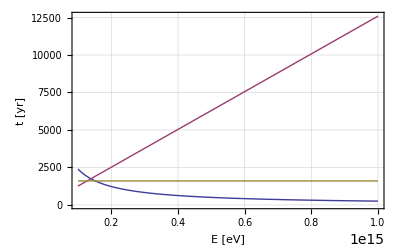

```mathematica
Plot[{(Ee*sec2yr)/(6.6*10^-4*B^2*(γ[Ee,Eerep])^2+Eerep*(5.5*10^17)*Tmcc^3*γ[Ee,Eerep]*Log[1+0.55*γ[Ee,Eerep]*Tmcc]/(1+25*Tmcc*γ[Ee,Eerep])*((1.4*γ[Ee,Eerep]*Tmcc)/(1+12*(γ[Ee,Eerep])^2*Tmcc^2)+1)+4*n*relec^2*β*c*(Log[183]-1/18)*Ee),(Ee*sec2yr)/(η*echar*csi^2*Bsi/(1.602*10^-19)),tsrn},{Ee,10^14,10^15},Frame->True,FrameLabel->{"E [eV]","t [yr]"},GridLines->Automatic,GridLinesStyle->GrayLevel[.9],Axes->False]
```

```mathematica
Solve[tacel[Ee]==(Ee*sec2yr)/(6.6*10^-4*B^2*(γ[Ee,Eerep])^2+Eerep*(5.5*10^17)*Tmcc^3*γ[Ee,Eerep]*Log[1+0.55*γ[Ee,Eerep]*Tmcc]/(1+25*Tmcc*γ[Ee,Eerep])*((1.4*γ[Ee,Eerep]*Tmcc)/(1+12*(γ[Ee,Eerep])^2*Tmcc^2)+1)+4*n*relec^2*β*c*(Log[183]-1/18)*Ee)&& Ee>0,Ee]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ee→4.50521×10^13}}

```mathematica
Eemax:=1.2705945544250278*^14
```

```mathematica
CALCULO ENERGIA MAXIMA PARA PROTONES
```

```mathematica
σ[Ep_]:=(34.3+1.88*Log[Ep*10^9]+0.25*(Log[Ep*10^9])^2)*10^-27   (*cm^2*)
dEpp[Ep_]:=0.65*c*n*σ[Ep]*HeavisideTheta[Ep - 1.22*10^9]*(Ep -Eprep) (*eV s^-1*)
tpp[Ep_]:=Ep*sec2yr/dEpp[Ep] (*yr*)
```

```mathematica
Plot[{(*tpp[Ep],*)tacel[Ep],tsrn},{Ep,10^15,10^16},Frame->True,FrameLabel->{"E [eV]","t [yr]"},GridLines->Automatic,GridLinesStyle->GrayLevel[.9],Axes->False]
```

```mathematica
NSolve[tacel[Ep]==tsrn ,Ep]
```

{{Ep→1.27059×10^14}}

```mathematica
Epmax:=1.2705945544250278*^14
```

```mathematica
CONSTANTES AE AP
```

```mathematica
Ap;

χ:= 0.1
Epmaxerg :=Epmax/erg2ev (*erg*)
Epminerg:=1*10^9/erg2ev(*erg*) (*La energia minima viene de que para que se produzcan colisiones p-p es necesario una energia mayor a 1GeV*)
Np[Ep_,α_,Epmaxerg_]:=Ep^-α ⅇ^(-Ep/Epmaxerg)
Aperg= (χ Esrn)/(1+Kp)3/(4π (Rout^3 - Rin^3)fvol)1/Integrate[Ep Np [Ep,α,Epmaxerg],{Ep,Epminerg,Epmaxerg}]
```

4.03727×10^-10

```mathematica
Ae;

Eemaxerg:=Eemax/erg2ev(*erg*)
Ne[Ee_,α_,Eemaxerg_]:=Ee^-α ⅇ^(-Ee/Eemaxerg)
Aeerg = (χ Esrn Kp)/(1+Kp)3/(4π (Rout^3 - Rin^3)fvol)1/NIntegrate[Ee Ne [Ee,α,Eemaxerg],{Ee,Eeminerg,Eemaxerg},PrecisionGoal->9,MaxRecursion->40]
```

2.73722×10^-11

```mathematica
e:=4.8*10^-10              (*StatCoulomb*)
Bcgs:=B                 (*Gauss=cm^(-1/2)g^(1/2)s^-1*)
Bsi:=B*T2G                         (*Tesla*)   
mc2:=511000                     (*eV*)
m:=9.1*10^-28                     (*g*)
c:=3*10^10                          (*cm/s*)
h:=6.63×10^-27               (*ergios s*)
Dsrn:=15000*pc2cm
f2L:=4*π*Dsrn^2  (*factor para pasar de flujo a luminosidad en tabla *)
V:=4/3*π*(Rout^3-Rin^3)   (*cm^3*)
CC:=1.85       (*viene de la aproximacion bessel*)
erg2ev:=1/ev2erg
ev2erg:=1.602*10^-12
β:=1/137
re:=2.8179*10^-13  (*cm*)
κ:=0.17
k:=8.61*10^-5;      (*eV/kelvin*)
T:=2.7 (*Kelvin*)
hev:=4.13*10^-15(*eV s*)
σT:=0.66 10^-24 (*cm^2*)
A:=Aeerg(*en cgs*)
Ae := A*(erg2ev )^(0.9)(*ev^0.9 cm^-3*)
Ap:=Aperg*(erg2ev )^(0.9)(*eV^0.9 cm^-3*);

(*Sincro*)
PP[Eph_,Ee_]:=(√3*π*e^3*Bcgs)/(h*m*c^2)*CC*(Eph/(3/(4π)*(e*h*Bcgs)/(m*c)*(Ee/(m*c^2))^2))^(1/3)*ⅇ^(-(Eph/(3/(4π)*(e*h*Bcgs)/(m*c)*(Ee/(m*c^2))^2))) 
NSinc[Ee_]:=A*Ee^-α*ⅇ^(-Ee/Eemaxerg)

P[Eph_]:=NIntegrate[PP[Eph,Ee]*NSinc[Ee],{Ee,Eeminerg,Eemaxerg},AccuracyGoal->12]

L[Eph_]:=Eph*P[Eph]*V*fvol

(*Brems*)
σ[Eγ_,Ee_]:=(4*β*re^2)/Eγ*ϕ[Eγ,Ee]*ev2erg (*cm^2 eV^-1*)
ϕ[Eγ_,Ee_]:=(1+(1-Eγ/Ee)^2-2/3*(1-Eγ/Ee))*Log[191]+1/9*(1-Eγ/Ee)
I1[Ee_]:=c/(4π)*Ae*Ee^-α*ⅇ^(-Ee/Eemax)
(*IC*)
ϵph[Eph_]:=Eph/Eerep
ϵγ[Eγ_]:=Eγ/Eerep
γ[Ee_]:= Ee/Eerep
x[Ee_,Eph_,Eγ_]:= ϵγ[Eγ]/(4ϵph[Eph] γ[Ee]^2(1-ϵγ[Eγ]/γ[Ee]))
PH[Ee_,Eph_,Eγ_]:=HeavisideTheta[1-x[Ee,Eph,Eγ]]HeavisideTheta[x[Ee,Eph,Eγ]-1/(4 γ[Ee]^2)]
f[Ee_,Eγ_,Eph_]:= (2x[Ee,Eph,Eγ] Log[x[Ee,Eph,Eγ]]+x[Ee,Eph,Eγ]+1-2 x[Ee,Eph,Eγ]^2+((4ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])^2(1-x[Ee,Eph,Eγ]))/(2 (1+4 ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])))PH[Ee,Eph,Eγ]
σIC[Ee_,Eγ_,Eph_]:=(3σT)/(4ϵph[Eph] γ[Ee]^2)f[Ee,Eγ,Eph]
Iic[Ee_]:=  Ae*Ee^-α* ⅇ^(-Ee/Eemax)
nBB[Eph_]:=(8*π)/(h*c)^3*Eph^2(ⅇ^(Eph/(k*T))-1)^-1*erg2ev

radio:={{5.4*10^-6, 8.4*10^-14*f2L}, {8.6*10^-6, 1.1*10^-13*f2L}}
ex:={{5.4*10^2, 4.42*10^-10*f2L}, {1.6*10^3, 4.05*10^-10*f2L}, {3.4*10^3, 3.12*10^-10*f2L}, {6.3*10^3, 2.29*10^-10*f2L}, {8.6*10^3, 1.69*10^-10*f2L}, {1.4*10^4, 1.30*10^-10*f2L}, {2.2*10^4, 8.04*10^-11*f2L}, {2.9*10^4, 4.55*10^-11*f2L}}
gamlat:={{7.4*10^8, 5.4*10^-12*f2L}, {1.8*10^9, 4.5*10^-12*f2L}, {4.6*10^9, 6.6*10^-12*f2L}, {1.4*10^10, 1.0*10^-11*f2L}, {3.4*10^10, 2.1*10^-11*f2L}, {1.0*10^11, 1.9*10^-11*f2L}, {2.5*10^11, 1.8*10^-11*f2L}}
gamhess:={{2.9*10^11, 4.4*10^-11*f2L}, {3.4*10^11, 3.3*10^-11*f2L}, {7.4*10^11, 2.6*10^-11*f2L}, {1.4*10^12, 3.4*10^-11*f2L}, {4.6*10^12, 2.8*10^-11*f2L}, {5.4*10^12, 2.4*10^-11*f2L}, {6.3*10^12, 2.0*10^-11*f2L}, {8.6*10^12, 1.5*10^-11*f2L}, {1.8*10^13, 9.9*10^-12*f2L}, {3.4*10^13, 1.2*10^-11*f2L}, {4.0*10^13, 3.6*10^-12*f2L}, {8.6*10^13, 2.3*10^-12*f2L}}

Show[Plot[{Log[10,L[10^(Eγ)/erg2ev]],Log10[(10^Eγ)^2*V*fvol*NIntegrate[n*σ[Eγ,Ee]*I1[Ee],{Ee,10^Eγ,∞},MaxRecursion->15]*ev2erg],Log[10,(10^Eγ)^2*fvolh*V*(2*c *n)/κ *Ap*10^-27 NIntegrate[1/(√(Eπ^2-Eπrep^2))(Eprep + Eπ/κ)^-α*ⅇ^(-(Eprep + Eπ/κ)/Epmax)*(34.3 +1.88 *Log[(Eprep + Eπ/κ) *10^12]+0.25 *Log[(Eprep + Eπ/κ)* 10^12]^2) ,{Eπ,(10^Eγ)+Eπrep^2/(4 *(10^Eγ)),10^16},MaxRecursion->20]/erg2ev],Log[10,(10^Eγ)^2*fvol*V*c/(4π)*NIntegrate[nBB[Eph]*σIC[Ee,10^Eγ,Eph]*Iic[Ee],{Ee,Eemin,10*Eemax},{Eph,0,100*k*T},AccuracyGoal->15]/erg2ev]},{Eγ,Log[10,10^-6],Log[10,10^15]},Axes->False, Frame->True,FrameLabel->{"Log_10[Eγ/eV]", "Log_10[L/(erg/s)]"}],ListPlot[{Log10[radio],Log10[ex],Log10[gamlat],Log10[gamhess]}],PlotRange->{{-6,16},{20,39}},PlotRangeClipping->True,Frame->True,GridLines->Automatic,GridLinesStyle->GrayLevel[.9],Axes->False]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate :: izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in Eph near {Ee, Eph} = {0.844124, 3.22008×10^-6}. NIntegrate obtained 1.51108×10^28 and 4.52912×10^27 for the integral and error estimates.

$Aborted